-Graphics3D-

-Graphics3D-

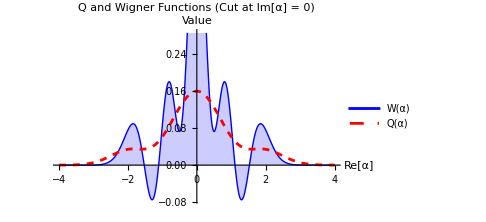

```mathematica
(*Definition of phase space coordinates*)(*r2= |α|^2=x^2+y^2*)r2[x_,y_]:=x^2+y^2

(*--------------------------------------------------------*)
(*1. Q function (Husimi) for statistical mixture (|0⟩⟨0|+ |4⟩⟨4|)/2*)
(*Q_M(α)=1/(2π)*(1+ |α|^8/24)*Exp[-|α|^2]*)

QFunctionMixed04[x_,y_]:=(1/(2*Pi))*(1+(r2[x,y]^4)/24)*Exp[-r2[x,y]]

(*--------------------------------------------------------*)
(*2. Wigner function for statistical mixture (|0⟩⟨0|+ |4⟩⟨4|)/2*)
(*W_M(α)=1/π*(1+L_4(4|α|^2))*Exp[-2|α|^2]*)

WignerFunctionMixed04[x_,y_]:=(1/Pi)*(1+LaguerreL[4,4*r2[x,y]])*Exp[-2*r2[x,y]]

(*--------------------------------------------------------*)
(*a) Plot Q function*)
(*Has rotational symmetry and positive peak at center*)

Plot3D[QFunctionMixed04[x,y],{x,-4,4},{y,-4,4},PlotRange->All,ColorFunction->"GrayYellowTones",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for Mixed State (|0⟩⟨0| + |4⟩⟨4|)/2 (Rotationally Symmetric)",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function*)
(*Has rotational symmetry but oscillates and has negative regions*)

Plot3D[WignerFunctionMixed04[x,y],{x,-4,4},{y,-4,4},PlotRange->All,(*Allow showing negative height range*)ColorFunction->"TemperatureMap",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for Mixed State (Negative Regions Confirm Nonclassicality)",Bold,14,Red],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice for clarity of oscillatory structure and negative regions*)

Plot[{WignerFunctionMixed04[x,0],QFunctionMixed04[x,0]},{x,-4,4},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 0)",Bold,14],PlotLegends->{"W(α)","Q(α)"},AxesLabel->{"Re[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis},ImageSize->Medium]
```